# Lab 9: Optimization -- Carter Colton

```mathematica
SetDirectory[NotebookDirectory[]] 
Clear["`*" ]
```

C:\Users\carte\OneDrive\Documents\Wolfram Mathematica

## Assignment 1: Local vs Global Minima

(a) Use FindMinimum to locate a local minimum of multimin  with x_0=1.0 as a starting point.  Set a variable minim equal to the x value where the minimum is located. (Hint: use [[2]] to access the “rule” for x that is returned. Then use slash-dot to turn that rule into a regular number.)
(b) Use NMinimize to find the global minimum of of multimin.

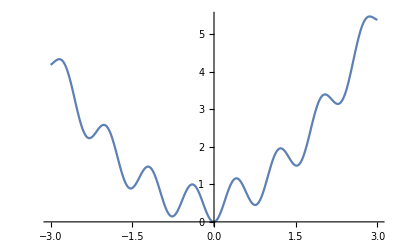

```mathematica
multimin[x_] := 0.5x^2+Sin[4*x]^2 +0.2 x
Plot[multimin[x],{x,-3,3}, PlotRange->All]
```

```mathematica
FindMinimum[multimin[x],{x,1.0}]
```

{0.450724,{x→0.755255}}

```mathematica
%[[2]]
```

{x→0.755255}

```mathematica
x/.%
```

0.755255

```mathematica
NMinimize[multimin[x],x];
%[[2]];
x/.%
```

-0.00606291

## Assignment 2: Unconstrained vs Constrained Minima

What you just found with NMinimize was an unconstrained minimum. Mathematica can also perform constrained minimization, where you specify additional conditions that must be true in addition to the function having  a minimum value. Consult the help file to see how to incorporate constraints.

(a) Use NMinimize to find the global minimum of of multimin, constrained by the condition x > 0.5.
(b) Repeat for the constraint x > 5. Be able to explain your results to the TA. Hint: plot the function around this value of x.

```mathematica
NMinimize[{multimin[x],x>0.5},x];
%[[2]];
x/.%
```

0.755255

```mathematica
NMinimize[{multimin[x],x>5.0},x];
%[[2]];
x/.%
```

5.

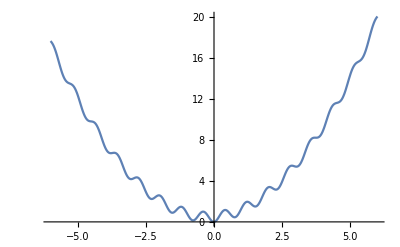

```mathematica
Plot[multimin[x],{x,-6,6}, PlotRange->All]
```

All the points above 5 for their x-coordinate are above the y-value of 5

## Assignment 3: A Basic Fit

Here’s a set of data for a damped harmonic oscillator. It’s a decaying sine wave, with a phase shift. Use FindFit to fit the data to this model function: f(x)=ae^-bx sin(cx+d). Find the parameters a, b, c, and d. As I did with the capacitor decay example, make a plot of the data (as points) along with the fitted function (as a curve).

```mathematica
xydata = {{0.0,5.71855},{0.2,7.29998},{0.4,6.37527},{0.6,2.92445},{0.8,-0.80489},{1.0,-3.97340},{1.2,-5.20427},{1.4,-4.55806},{1.6,-2.16204},{1.8,0.65275},{2.0,2.91818},{2.2,3.67343},{2.4,3.25607},{2.6,1.43566},{2.8,-0.50996},{3.0,-1.94053},{3.2,-2.80186},{3.4,-2.19941},{3.6,-1.30169},{3.8,0.38208},{4.0,1.40752},{4.2,1.90920},{4.4,1.87848},{4.6,0.72315},{4.8,-0.42480},{5.0,-1.11011},{5.2,-1.36038},{5.4,-1.08811},{5.6,-0.66390},{5.8,0.12442},{6.0,0.78261},{6.2,1.17796},{6.4,0.83673},{6.6,0.60683},{6.8,-0.25237},{7.0,-0.63443},{7.2,-0.86788},{7.4,-0.68180},{7.6,-0.23394},{7.8,0.12773},{8.0,0.29089},{8.2,0.45893},{8.4,0.17779},{8.6,0.30576},{8.8,-0.05089},{9.0,-0.15026},{9.2,-0.35048},{9.4,-0.06596},{9.6,-0.22677},{9.8,0.15325},{10.0,0.18327}};
```

```mathematica
fitthefunction = a*E^(-b*x)*Sin[c*x+d];
fitresults =FindFit[xydata,fitthefunction,{a,b,c,d},x];
besta = a/.fitresults[[1]]
bestb =b/.fitresults[[2]]
bestc=c/.fitresults[[3]]
bestd=d/.fitresults[[4]]
```

7.99388

0.332938

3.14182

0.776409

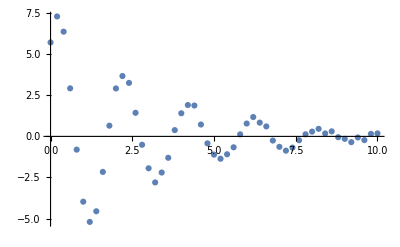

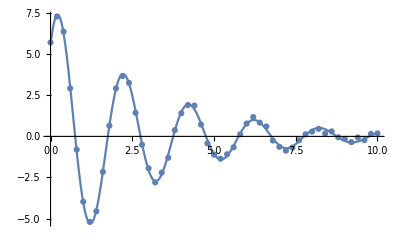

```mathematica
plot1 = ListPlot[xydata, PlotRange->All]
plot2 = Plot[fitthefunction/. fitresults,{x,0,10}, PlotRange->All];
Show[plot1,plot2]
```

## Assignment 4: Capacitor Again: Trying Other V0 and k Values

Create another trial function (modeldecay, with different values of V0 and k), and compute the squared error. Do this several times, so that you become completely convinced that our “bestV0” and “bestk” values really do give the least amount of squared error.

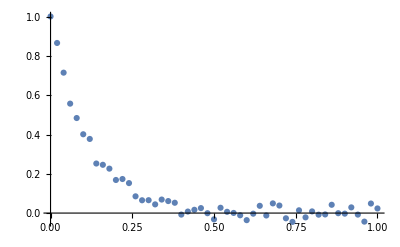

```mathematica
capdata = Import["capacitor.csv"] ;
plot1 = ListPlot[capdata, PlotRange->All]
```

```mathematica
modeldecay= V0 Exp[-k*t];
fitresults = FindFit[capdata,modeldecay,{V0, k},t];
bestV0 = V0 /. fitresults[[1]]
bestk = k /. fitresults[[2]]
decaytime = (1/bestk);
```

1.00792

8.90052

```mathematica
xvals =(capdata //Transpose) [[1]];  (* the column of x-values (time) *)
yvals =(capdata //Transpose )[[2]];  (* the column of y-values *)

trial1[t_] = modeldecay /. {V0->bestV0,k->bestk}   (* a specific trial function *)
yvals1 = Table[trial1[t],{t,xvals}]  (* the y-values at the given x-values, for our best fit trial function *)
squaredError1 = Total[ (yvals - yvals1)^2]
```

1.00792 ⅇ^(-8.90052 t)

{1.00792,0.843564,0.706007,0.590881,0.494528,0.413887,0.346396,0.289911,0.242636,0.20307,0.169956,0.142242,0.119047,0.0996348,0.0833877,0.06979,0.0584096,0.048885,0.0409135,0.0342419,0.0286582,0.023985,0.0200739,0.0168005,0.0140609,0.011768,0.00984907,0.00824302,0.00689886,0.00577389,0.00483236,0.00404437,0.00338487,0.00283291,0.00237096,0.00198434,0.00166076,0.00138994,0.00116329,0.000973597,0.000814837,0.000681964,0.000570759,0.000477687,0.000399793,0.0003346,0.000280038,0.000234373,0.000196155,0.000164169,0.000137398}

0.0312993

```mathematica
trial1[t_] = modeldecay /. {V0->5,k->10};   (* a specific trial function *)
yvals1 = Table[trial1[t],{t,xvals}];  (* the y-values at the given x-values, for our best fit trial function *)
squaredError1 = Total[ (yvals - yvals1)^2]
```

47.2337

```mathematica
trial1[t_] = modeldecay /. {V0->3,k->4};   (* a specific trial function *)
yvals1 = Table[trial1[t],{t,xvals}];  (* the y-values at the given x-values, for our best fit trial function *)
squaredError1 = Total[ (yvals - yvals1)^2]
```

37.6989

```mathematica
trial1[t_] = modeldecay /. {V0->.5,k->1};   (* a specific trial function *)
yvals1 = Table[trial1[t],{t,xvals}];  (* the y-values at the given x-values, for our best fit trial function *)
squaredError1 = Total[ (yvals - yvals1)^2]
```

3.37026

```mathematica
trial1[t_] = modeldecay /. {V0->0.005,k->0.001};   (* a specific trial function *)
yvals1 = Table[trial1[t],{t,xvals}];  (* the y-values at the given x-values, for our best fit trial function *)
squaredError1 = Total[ (yvals - yvals1)^2]
```

3.36235

All the attempts that I made were above the bestV0 and bestk

## Assignment 5: Find the Minimum of the Squared Error Function

Use FindMinimum to locate the minimum of that squaredErrorx function. Compare your results to the “bestV0” and “bestk” values found by the FindFit function.

```mathematica
trialx[t_,V0_,k_] = modeldecay ;
yvalstrialx[V0_,k_] := Table[trialx[t,V0,k],{t,xvals}];
squaredErrorx[V0_,k_] := Total[ (yvals - yvalstrialx[V0,k])^2];
squaredErrorx[bestV0,bestk]   (* just a test *)
```

0.0312993

```mathematica
Plot3D[squaredErrorx[V0,k],{V0,0,1.9},{k,6,25}]
```

-Graphics3D-

```mathematica
minimum=FindMinimum[squaredErrorx[V0,k],{V0,k}]
```

{0.0312993,{V0→1.00792,k→8.90052}}

```mathematica
minimum[[2]][[1]];
calculatedbestV0=V0/.%
bestV0
```

1.00792

1.00792

```mathematica
minimum[[2]][[2]];
calculatedbestk=k/.%
bestk
```

8.90052

8.90052

```mathematica
calculatedminimum=minimum[[1]]
```

0.0312993

## Assignment 6: Absolute Value Error

Repeat the procedure you just went through in the previous section to determine the values of V0 and k that minimize the absolute value error. Define the cost to be the absolute value of the difference between your data point and the trial function point, summed over all points. (You don’t have to make a plot unless you want to.) Compare the values of V0 and k that this method yields to the least squares method values. They should be close, but not quite the same. Hint: When I did this, I found that the FindMinimum command generated an error message. Switching to a different Method allowed it to work without errors.

```mathematica
trialabs[t_,V0_,k_] = modeldecay ;
yvalstrialabs[V0_,k_] := Table[trialabs[t,V0,k],{t,xvals}];
absError[V0_,k_] := Total[ Abs[yvals - yvalstrialabs[V0,k]]];
absError[bestV0,bestk]
```

1.04373

```mathematica
minimumabs=FindMinimum[absError[V0,k],{V0,k},Method->"PrincipalAxis"]
```

{1.0392,{V0→1.00175,k→8.90946}}

Remember that the least square values were equal to bestV0 and bestk

```mathematica
minimumabs[[2]][[1]];
calculatedabsV0=V0/.%
bestV0
```

1.00175

1.00792

```mathematica
minimumabs[[2]][[2]];
calculatedabsk=k/.%
bestk
```

8.90946

8.90052

```mathematica
minimumabs[[1]]
```

1.0392

## Assignment 7: Using “Fit”

Here is some made-up data. (Download linearfitfunction.csv from the Physics 230 website and put it in your active directory.)

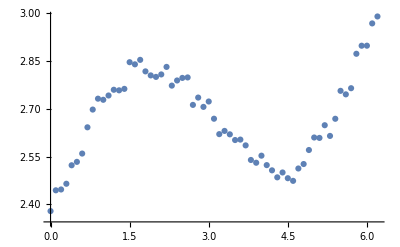

```mathematica
newxydata=Import["linearfitfunction.csv"];
plot1=ListPlot[newxydata]
```

(a) Use Fit to fit it to this function: y=C_1 sin(x) + C_2 e^(0.1x)+C_3. That is, determine the values of C_1, C_2, C_3 that give it the least squared error. Then plot the fit along with the data.
(b) Use FindFit to do the same fit, and show that the fitted parameters have the same value.

```mathematica
fitfornewxy=Fit[newxydata,{1,Sin[x],E^(0.1*x)},x]
```

1.61468+0.763525 ⅇ^(0.1 x)+0.308532 Sin[x]

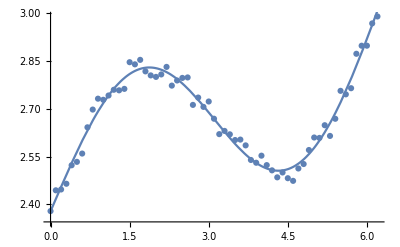

```mathematica
plot2=Plot[fitfornewxy,{x,0,10}];
Show[plot1,plot2]
```

```mathematica
Clear[c1,c2,c3]
```

```mathematica
findfitexpression=c3+c1*Sin[x]+c2*E^(.1*x)
```

c3+c2 ⅇ^(0.1 x)+c1 Sin[x]

```mathematica
fitresults1=FindFit[newxydata,findfitexpression,{c1,c2,c3},x]
```

{c1→0.308532,c2→0.763525,c3→1.61468}

```mathematica
plot3=Plot[findfitexpression/.fitresults1,{x,0,10},PlotRange->All];
Show[plot1,plot3]
```

-Graphics-

## Assignment 8: Fourier Series Representation of a Square Wave

(a) Create a list of {x,y} data by “sampling” the function y(x) from -10 to 10 in steps of 0.01. Use ListPlot to view your data, to make sure it looks like the y(x) plot above.
(b) Create a list of 50 basis functions:  {sin(k_0 x),sin(2 k_0 x), sin(3 k_0 x), ..., sin(50 k_0 x)}
(c) Do a linear fit of your sampled data over the set of basis functions. Plot the resulting function.
(d) Repeat for 5 basis functions, and for 500 basis functions. Notice as you increase the number of basis functions the fit does a better and better job of reproducing the square wave.

```mathematica
Clear[y]
```

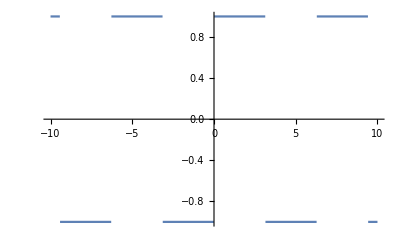

```mathematica
y[x_]:=If[Sin[x]>0,1,-1];
Plot[y[x],{x,-10,10}]
```

```mathematica
sampledata=Table[{x,y[x]},{x,-10,10,0.01}];
```

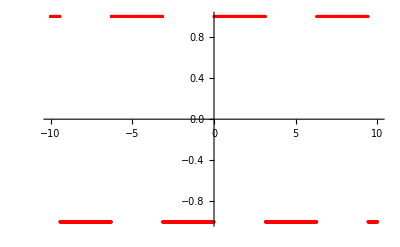

```mathematica
sampledataplot=ListPlot[sampledata,PlotStyle->Red]
```

```mathematica
k0=1
```

1

```mathematica
sindata=Table[Sin[n*k0*x],{n,1,50}]
```

{Sin[x],Sin[2 x],Sin[3 x],Sin[4 x],Sin[5 x],Sin[6 x],Sin[7 x],Sin[8 x],Sin[9 x],Sin[10 x],Sin[11 x],Sin[12 x],Sin[13 x],Sin[14 x],Sin[15 x],Sin[16 x],Sin[17 x],Sin[18 x],Sin[19 x],Sin[20 x],Sin[21 x],Sin[22 x],Sin[23 x],Sin[24 x],Sin[25 x],Sin[26 x],Sin[27 x],Sin[28 x],Sin[29 x],Sin[30 x],Sin[31 x],Sin[32 x],Sin[33 x],Sin[34 x],Sin[35 x],Sin[36 x],Sin[37 x],Sin[38 x],Sin[39 x],Sin[40 x],Sin[41 x],Sin[42 x],Sin[43 x],Sin[44 x],Sin[45 x],Sin[46 x],Sin[47 x],Sin[48 x],Sin[49 x],Sin[50 x]}

```mathematica
sinplotfit=Fit[sampledata,sindata,x];
```

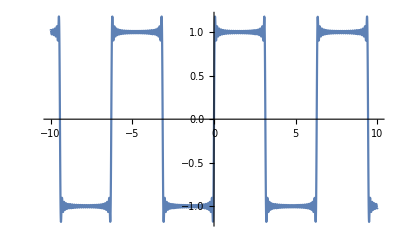

```mathematica
sinplot=Plot[sinplotfit,{x,-10,10}]
```

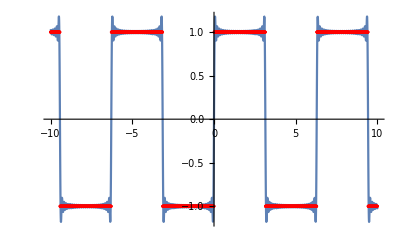

```mathematica
Show[sinplot,sampledataplot]
```

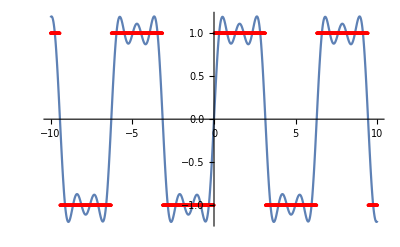

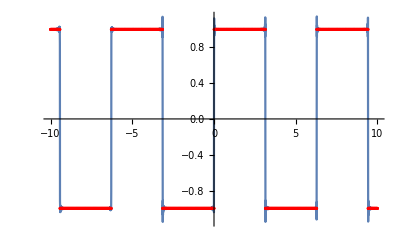

```mathematica
sindata5=Table[Sin[n*k0*x],{n,1,5}];
sindata500=Table[Sin[n*k0*x],{n,1,500}];
sinplotfit5=Fit[sampledata,sindata5,x];
sinplotfit500=Fit[sampledata,sindata500,x];
sinplot5=Plot[sinplotfit5,{x,-10,10}];
sinplot500=Plot[sinplotfit500,{x,-10,10}];
Show[sinplot5,sampledataplot]
Show[sinplot500,sampledataplot]
```

## Assignment 9: Fit with Weighted Uncertainties

{{1,13.8425,1.31387},{2,10.5968,1.18028},{3,8.7823,1.08637},{4,7.58313,1.01296},{5,6.79541,0.95812},{6,6.11933,0.90573},{7,4.97807,0.80252},{8,4.07347,0.70225},{9,4.18155,0.71534},{10,3.5588,0.63471},{11,3.36735,0.60706},{12,3.08605,0.56345},{13,3.31048,0.59855},{14,3.10261,0.56612},{15,2.35429,0.42812},{16,2.9631,0.54312},{17,2.89468,0.53144},{18,2.35118,0.42746},{19,2.65534,0.48829},{20,2.74187,0.50432},{21,2.91863,0.53556},{22,2.70865,0.49823},{23,3.04143,0.55616},{24,2.8579,0.52504},{25,2.73896,0.50379},{26,2.99886,0.54912},{27,2.75556,0.50681},{28,2.36882,0.4312},{29,2.58676,0.4752},{30,2.20919,0.39631},{31,2.17119,0.38764}}

{{1,13.8425},{2,10.5968},{3,8.7823},{4,7.58313},{5,6.79541},{6,6.11933},{7,4.97807},{8,4.07347},{9,4.18155},{10,3.5588},{11,3.36735},{12,3.08605},{13,3.31048},{14,3.10261},{15,2.35429},{16,2.9631},{17,2.89468},{18,2.35118},{19,2.65534},{20,2.74187},{21,2.91863},{22,2.70865},{23,3.04143},{24,2.8579},{25,2.73896},{26,2.99886},{27,2.75556},{28,2.36882},{29,2.58676},{30,2.20919},{31,2.17119}}

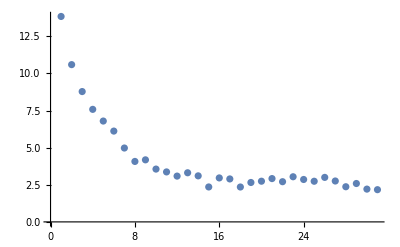

```mathematica
xysigma = Import["datawitherrorbars.csv"]
xydata = xysigma   /. {x_,y_,s_}  -> {x,y}   (* Notice this line!! Explained below. *)
ListPlot[xydata]
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

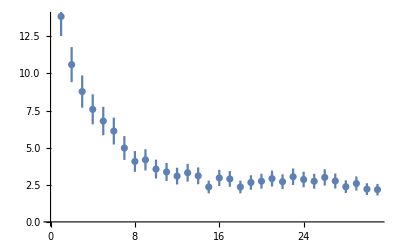

```mathematica
Needs["ErrorBarPlots`"]
oddformat = xysigma /. {x_,y_,s_}  -> {{x, y},ErrorBar[s]}  ; 
errorbarplot=ErrorListPlot[oddformat, PlotRange->All, AxesOrigin->{0,0}]
model[x_] := a*Exp[-x/b] +c;
(*errorbarfit=FindFit[oddformat,model[x],{a,b,c},x];
Show[errorbarplot,errorbarfit]*)
```

(a) At this point let me turn it over to you. We’ll need the list of uncertainty numbers all by themselves for the next step, so use my trick to transform xysigma into just a list of s values (the third column), and call the result uncertainty.

(b) Now fit the xydata using NonlinearModelFit with Weights → 1/uncertainty^2 as an option. The result of the NonlinearModelFit is a FittedModel object; give it the name nlm (standing for “nonlinear model”).

Behind the scenes: The Weights → 1/uncertainty^2 option has told Mathematica to use a new cost function, somewhat like the problem above where you used the absolute value instead of the squared error. In this case, the  Weights specifier tells Mathematica to use a “weighted least squares” error function, which is computed as:  cost=∑ _n (w_n(y_n-f(x_n)))^2.  Here w_n is the weighting factor for the n^th term. The   → 1/uncertainty^2   part, with your definition of uncertainty from part (a) means that you want w_n= 1/s_n^2, i.e. you want each point weighted by the inverse square of its uncertainty. Thus we increase the importance of data points with small uncertainties and decrease the importance of data points with large uncertainties. We could have weighted things differently, but 1/uncertainty^2 turns out to be exactly the right thing to do if your s_n uncertainty values are standard deviations (due to Aitken’s extension of the Gauss-Markov thorem, if you care).

(c) Assuming that the previous step was executed correctly, you can now use nlm to study many useful properties of the fit.  Evaluate the cell below and observe that not only has it properly accounted for the "error bars" at the points, it has also produced a list of uncertainties for your fitted parameters (i.e. "ParameterErrors"). (Exactly how the parameter uncertainties are estimated is beyond the scope of this course.) See the "Scope" section of the NonlinearModelFit reference page for a complete list of the properties that can be displayed for nonlinear model fits.

```mathematica
sdata=xysigma/.{x_,y_,s_}  -> s
```

{1.31387,1.18028,1.08637,1.01296,0.95812,0.90573,0.80252,0.70225,0.71534,0.63471,0.60706,0.56345,0.59855,0.56612,0.42812,0.54312,0.53144,0.42746,0.48829,0.50432,0.53556,0.49823,0.55616,0.52504,0.50379,0.54912,0.50681,0.4312,0.4752,0.39631,0.38764}

```mathematica
nlm=NonlinearModelFit[xydata,model[x],{a,b,c},x,Weights -> 1/sdata^2]
```

FittedModel[2.53406+14.0799 ⅇ^(-0.253565 x)]

2.53406+14.0799 ⅇ^(-0.253565 x)

{a→14.0799,b→3.94375,c→2.53406}

{0.781419,0.238577,0.0681785}

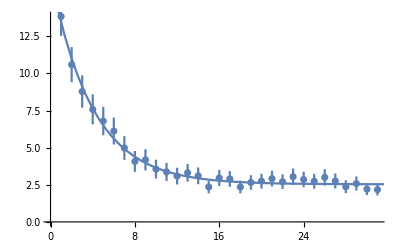

```mathematica
nlm["BestFit"]
nlm["BestFitParameters"]
nlm["ParameterErrors"]
Show[errorbarplot, Plot[nlm["BestFit"],{x,0,32}, PlotRange->All]]
```

## Assignment 10: Fitting Variable Star Data

The file NGC6811-35.csv, available on the Physics 230 website, is data digitized from a paper by Michael B. Rose and Eric G. Hintz of BYU entitled “A search for low-amplitude variability in six open clusters using the robust median statistic”, published in The Astronomical Journal, vol. 134, pp 2067-2078, in Nov 2007. The file contains data points representing the magnitude of the star NGC 6811-35 as a function of time. The magnitude of a star is proportional to the log of its brightness. (I.e., brightness = 10^magnitude.) The first column in the file is the time in hours at which the star was observed. The second column is its magnitude.

(a) Convert the y-axis to brightness, then ListPlot the data. (The x-axis is time.)
(b) You should see a sinusoidal variation to the brightness, albeit with a lot of noise. Fit the data to a function:  y=y_0+Acos(2πt/period - ϕ), where y_0, A, period, and ϕ are fitting parameters. Use a NonlinearModelFit so that you can also obtain the uncertainties in the parameters. Plot your data and the fit on the same graph to make sure your fit is reasonable.

Note: For reasons I couldn’t determine, Mathematica is super-picky about the functional form needed to fit this particular data. Using  + ϕ  instead of   - ϕ , for example, caused the fit to fail completely. I had similar problems when I tried Sin instead of Cos (even though they should be equivalent if given an appropriate phase shift), and when I tried to use ω instead of 2π/period. (I mentioned that nonlinear fits could be tricky!) So be sure to use the fitting function exactly as specified above.

```mathematica
stardata=Import["C:\\Users\\carte\\OneDrive\\Documents\\Wolfram Mathematica\\NGC6811-35.csv"];
```

```mathematica
stardatabrightness={#[[1]],10^(#[[2]])}&/@stardata
```

{{0,1.18361×10^10},{0.0506757,1.17123×10^10},{0.0743243,1.16459×10^10},{0.0945946,1.14359×10^10},{0.10473,1.16426×10^10},{0.125,1.16492×10^10},{0.135135,1.1729×10^10},{0.152027,1.16923×10^10},{0.179054,1.16824×10^10},{0.199324,1.16857×10^10},{0.202703,1.18092×10^10},{0.226351,1.16128×10^10},{0.246622,1.18361×10^10},{0.256757,1.17891×10^10},{0.277027,1.16824×10^10},{0.297297,1.19579×10^10},{0.304054,1.16957×10^10},{0.331081,1.19002×10^10},{0.351351,1.205×10^10},{0.368243,1.20981×10^10},{0.371622,1.1907×10^10},{0.39527,1.22052×10^10},{0.415541,1.19579×10^10},{0.425676,1.22469×10^10},{0.442568,1.2394×10^10},{0.466216,1.21947×10^10},{0.47973,1.21118×10^10},{0.493243,1.21532×10^10},{0.516892,1.19443×10^10},{0.523649,1.19987×10^10},{0.550676,1.18059×10^10},{0.567568,1.19715×10^10},{0.587838,1.18126×10^10},{0.601351,1.19104×10^10},{0.614865,1.20226×10^10},{0.641892,1.17123×10^10},{0.652027,1.19987×10^10},{0.662162,1.20843×10^10},{0.689189,1.18429×10^10},{0.692568,1.19885×10^10},{0.719595,1.19545×10^10},{0.736486,1.16923×10^10},{0.746622,1.20158×10^10},{0.77027,1.16857×10^10},{0.787162,1.1739×10^10},{0.807432,1.15963×10^10},{0.814189,1.17757×10^10},{0.834459,1.1759×10^10},{0.85473,1.16857×10^10},{0.871622,1.157×10^10},{0.891892,1.14489×10^10},{1.28716,1.15077×10^10},{1.29392,1.1626×10^10},{1.31757,1.1759×10^10},{1.3277,1.15667×10^10},{1.34122,1.1689×10^10},{1.36824,1.1907×10^10},{1.38514,1.18059×10^10},{1.40878,1.15667×10^10},{1.4223,1.17523×10^10},{1.44257,1.17824×10^10},{1.44595,1.1593×10^10},{1.46622,1.18631×10^10},{1.48649,1.19239×10^10},{1.50676,1.18429×10^10},{1.51014,1.188×10^10},{1.54054,1.17323×10^10},{1.55743,1.16857×10^10},{1.56757,1.18597×10^10},{1.58108,1.19545×10^10},{1.61149,1.19036×10^10},{1.62162,1.20637×10^10},{1.63514,1.20672×10^10},{1.65541,1.18597×10^10},{1.67905,1.17023×10^10},{1.70608,1.17858×10^10},{1.72973,1.17958×10^10},{1.72973,1.18597×10^10},{1.76689,1.14457×10^10},{1.78041,1.17925×10^10},{1.78378,1.17056×10^10},{1.82095,1.18361×10^10},{1.8277,1.16327×10^10},{1.84797,1.18665×10^10},{1.85473,1.19613×10^10},{1.875,1.15404×10^10},{1.90203,1.15109×10^10},{1.90541,1.15536×10^10},{1.92568,1.14979×10^10},{1.97635,1.12681×10^10},{2.00338,1.16227×10^10},{2.01351,1.13195×10^10},{2.02703,1.15011×10^10},{2.05068,1.13743×10^10},{2.06081,1.13098×10^10},{2.0777,1.13614×10^10},{2.10473,1.15898×10^10},{2.10811,1.13324×10^10},{2.4223,1.1636×10^10},{2.43581,1.19715×10^10},{2.45946,1.19681×10^10},{2.47297,1.17323×10^10},{2.48649,1.18193×10^10},{2.51014,1.17958×10^10},{2.52703,1.18901×10^10},{2.54054,1.19341×10^10},{2.56419,1.15437×10^10},{2.5777,1.18867×10^10},{2.58446,1.20124×10^10},{2.61149,1.17757×10^10},{2.63176,1.17223×10^10},{2.64189,1.19885×10^10},{2.65541,1.18395×10^10},{2.67568,1.20432×10^10},{2.69257,1.18698×10^10},{2.71284,1.18429×10^10},{2.72973,1.19919×10^10},{2.75,1.188×10^10},{2.75676,1.20158×10^10},{2.77703,1.21982×10^10},{2.80068,1.1593×10^10},{2.81081,1.1719×10^10},{2.83108,1.17657×10^10}}

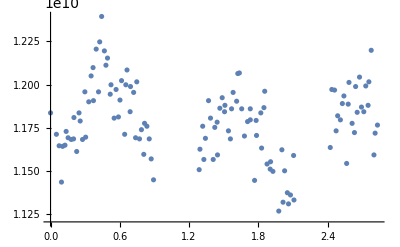

```mathematica
stardatabrightnessplot=ListPlot[stardatabrightness]
```

```mathematica
modely[t_]:=y0+A*Cos[((2*Pi*t)/period)-phi];
```

```mathematica
nlm2=NonlinearModelFit[stardatabrightness,modely[t],{y0,A,period,phi},t]
```

FittedModel[1.17105×10^10-2.37931×10^8 Cos[433.207-5.77026 t]]

1.17105×10^10-2.37931×10^8 Cos[433.207-5.77026 t]

{y0→1.17105×10^10,A→-2.37931×10^8,period→1.08889,phi→433.207}

{1.6705×10^7,2.36787×10^7,0.0198385,0.151963}

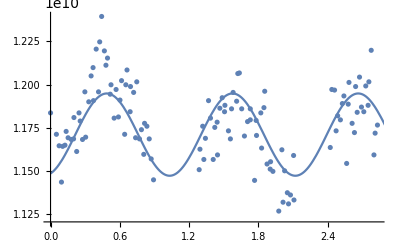

```mathematica
nlm2["BestFit"]
nlm2["BestFitParameters"]
nlm2["ParameterErrors"]
Show[stardatabrightnessplot, Plot[nlm2["BestFit"],{t,0,5}, PlotRange->All]]
```